--- Automatic Branch Recovery ---

w_original = (20 ⅇ^(-1/2 ⅈ (-2 Arg[10+x-ⅈ y]+Arg[300-x (20+x)-y^2]+2 Arg[√(300-x (20+x)-y^2)+ⅈ √((10+x)^2+y^2)])) (100+x (20+x)+y^2-ⅈ ⅇ^(1/2 ⅈ Arg[300-x (20+x)-y^2]) √((10+x)^2+y^2) ((-300+x (20+x)+y^2)^2)^(1/4)))/((10+x+ⅈ y) √((10+x)^2+y^2) ((-300+x (20+x)+y^2)^2)^(1/4) √(100+x (20+x)+y^2+√((-300+x (20+x)+y^2)^2)+2 √((10+x)^2+y^2) ((-300+x (20+x)+y^2)^2)^(1/4) Sin[1/2 Arg[300-x (20+x)-y^2]]))

--- Visualizing the Physical Fields ---

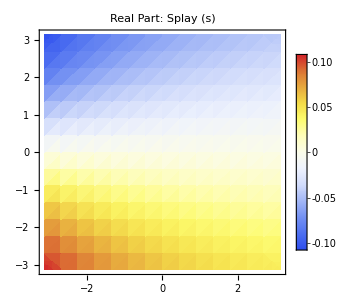
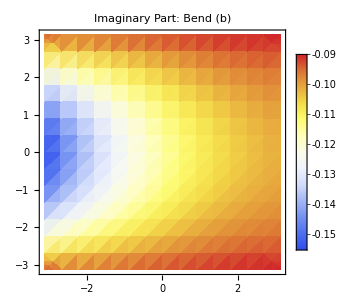

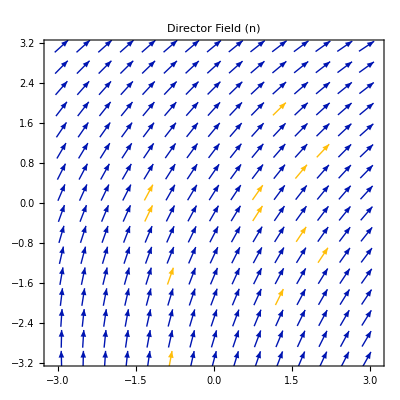

--- Verifying Algebraic Recovery ---

$Aborted

Calculated Laplacian (Δθ) = ((-1-x/10) (1+x/10))/(800 √((1+x/10)^2+y^2/100) (1+1/4 (-(1+x/10)^2-y^2/100))^(3/2))-y^2/(80000 √((1+x/10)^2+y^2/100) (1+1/4 (-(1+x/10)^2-y^2/100))^(3/2))+(1+x/10)^2/(200 ((1+x/10)^2+y^2/100)^(3/2) √(1+1/4 (-(1+x/10)^2-y^2/100)))+y^2/(20000 ((1+x/10)^2+y^2/100)^(3/2) √(1+1/4 (-(1+x/10)^2-y^2/100)))-1/(100 √((1+x/10)^2+y^2/100) √(1+1/4 (-(1+x/10)^2-y^2/100)))

Assigned Branch Sign = -Sign[((-1-x/10) (1+x/10))/(800 √((1+x/10)^2+y^2/100) (1+1/4 (-(1+x/10)^2-y^2/100))^(3/2))-y^2/(80000 √((1+x/10)^2+y^2/100) (1+1/4 (-(1+x/10)^2-y^2/100))^(3/2))+(1+x/10)^2/(200 ((1+x/10)^2+y^2/100)^(3/2) √(1+1/4 (-(1+x/10)^2-y^2/100)))+y^2/(20000 ((1+x/10)^2+y^2/100)^(3/2) √(1+1/4 (-(1+x/10)^2-y^2/100)))-1/(100 √((1+x/10)^2+y^2/100) √(1+1/4 (-(1+x/10)^2-y^2/100)))]

$Aborted

$Aborted

Real part of Error: realDiff

Imaginary part of Error: imagDiff

FAILED. Check assumptions or formula.

$Aborted

נשמר בהצלחה! התיקייה עם כל התמונות ומסמך ההסבר נמצאת בנתיב:
C:\Users\yarde\OneDrive - weizmann.ac.il\שולחן העבודה\WSOS\Efi efrati\עבודה עם אפי\סימולציה נוסחת תאימות\N_2_R=5

```mathematica
ClearAll["Global`*"];
ClearAll["Global`*"];
(* ==========================================================*)
(*1*)
(* ==========================================================*)
twoDz[f_]:=D[f,x]-I*D[f,y];
twoDzbar[f_]:=D[f,x]+I*D[f,y];

conj[expr_]:=ComplexExpand[Conjugate[expr],TargetFunctions->{Re,Im}];
absSq[expr_]:=Expand[expr*conj[expr]];

Print[Style["--- Automatic Branch Recovery ---",Bold,16,Blue]];

(* ==========================================================*)
(*2*)
(* ==========================================================*)

R=5;

rho[r_,x_,y_]:=Sqrt[(1+x/(2 r))^2+(y/(2 r))^2];
phi[r_,x_,y_]:=ArcTan[1+x/(2 r),-y/(2 r)];
beta[r_,x_,y_]:=ArcSin[rho[r,x,y]/2];

theta[x_,y_]:=phi[R,x,y]+Pi/2-beta[R,x,y];
n0=Cos[theta[x,y]]+I Sin[theta[x,y]];

wOriginal=twoDz[n0]//ComplexExpand;
Print[Style["w_original = ",Bold,14,Blue],FullSimplify[wOriginal]];
(* ==========================================================*)
(*3*)
(* ==========================================================*)
Print["\n",Style["--- Visualizing the Physical Fields ---",Bold,14,Blue]];

splay=ComplexExpand[Re[wOriginal]];
bend=ComplexExpand[Im[wOriginal]];

plotS=DensityPlot[splay,{x,-Pi,Pi},{y,-Pi,Pi},PlotLabel->"Real Part: Splay (s)",ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->300];

plotB=DensityPlot[bend,{x,-Pi,Pi},{y,-Pi,Pi},PlotLabel->"Imaginary Part: Bend (b)",ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->300];

Print[Row[{plotS,plotB}]];

nx=ComplexExpand[Re[n0]];
ny=ComplexExpand[Im[n0]];
plotN=VectorPlot[{nx,ny},{x,-Pi,Pi},{y,-Pi,Pi},PlotLabel->"Director Field (n)",VectorStyle->Black,VectorScale->{Tiny,Automatic,None},ImageSize->400];

Print[plotN];

(* ==========================================================*)
(*4.*)
(* ==========================================================*)
Print["\n",Style["--- Verifying Algebraic Recovery ---",Bold,14,Blue]];

wAbsSq=absSq[wOriginal];
wDzbar=twoDzbar[wOriginal]//ComplexExpand;
wDzbarBar=conj[wDzbar];
wDzbarAbsSq=absSq[wDzbar];

R2=wDzbarAbsSq-wAbsSq^2//FullSimplify;
Rexpr=Sqrt[R2];

(* ===ן===*)
laplacianTheta=D[theta[x,y],{x,2}]+D[theta[x,y],{y,2}];
branchSign=-Sign[laplacianTheta];

Print["Calculated Laplacian (Δθ) = ",laplacianTheta];
Print["Assigned Branch Sign = ",branchSign];

(**)
nRecovered=(-wAbsSq+branchSign*I*Rexpr)/wDzbarBar;

(* ==========================================================*)
(*5*)
(* ==========================================================*)
diff=nRecovered-n0;

(**)
realDiff=FullSimplify[ComplexExpand[Re[diff]],Assumptions->{x>-Pi,x< Pi,y∈Reals}];
imagDiff=FullSimplify[ComplexExpand[Im[diff]],Assumptions->{x>-Pi,x<Pi,y∈Reals}];

Print["Real part of Error: ",realDiff];
Print["Imaginary part of Error: ",imagDiff];

If[realDiff===0&&imagDiff===0,Print[Style["SUCCESS! n_recovered matches n_original perfectly on the correct branch.",Bold,16,Darker[Green]]],Print[Style["FAILED. Check assumptions or formula.",Bold,16,Red]]];
(* ==========================================================*)(*6. שמירה אוטומטית של הגרפים ומסמך הערכים בתיקייה מסודרת*)(* ==========================================================*)(*שם התיקייה והקבצים עבור הדוגמה הנוכחית-שנה רק את השם הזה בין הרצה להרצה*)exampleName="N_2_R=5";

(*יצירת התיקייה באותו מיקום שבו שמור קובץ ה-Mathematica (או בתיקיית העבודה)*)
baseDir=Quiet@Check[NotebookDirectory[],Directory[]];
outputDir=FileNameJoin[{baseDir,exampleName}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];

(*1. שמירת שלוש התמונות בשמות הנכונים*)
Export[FileNameJoin[{outputDir,exampleName<>"_Director_Field_n.png"}],plotN,ImageResolution->300];
Export[FileNameJoin[{outputDir,exampleName<>"_Real_Part_Splay_s.png"}],plotS,ImageResolution->300];
Export[FileNameJoin[{outputDir,exampleName<>"_Imaginary_Part_Bend_b.png"}],plotB,ImageResolution->300];

(*2. יצירת מסמך ההסבר עם כל הערכים של הדוגמה ושמירתו בתיקייה*)
summaryText=StringJoin["==========================================================\n","הסבר ופירוט הערכים בדוגמה: ",exampleName,"\n","==========================================================\n\n","1. פונקציית הזווית (theta[x, y]):\n   ","theta(x, y) = ",ToString[theta[x,y],InputForm],"\n\n","2. שדה הדירקטור המקורי (n0 = Cos[theta] + I*Sin[theta]):\n   ","n0 = ",ToString[n0,InputForm],"\n\n","3. שדה העקמומיות המרוכב (w_original = 2*d_z(n0)):\n   ","w = ",ToString[wOriginal,InputForm],"\n\n","4. החלק הממשי - התבדרות (Real Part: Splay, s = Re[w]):\n   ","s(x, y) = ",ToString[splay,InputForm],"\n\n","5. החלק המדומה - כיפוף (Imaginary Part: Bend, b = Im[w]):\n   ","b(x, y) = ",ToString[bend,InputForm],"\n\n","6. גודל העזר בריבוע (R^2 = |2*d_zbar(w)|^2 - |w|^4):\n   ","R^2 = ",ToString[R2,InputForm],"\n\n","7. הלפלסיאן של הזווית (Laplacian = theta_xx + theta_yy):\n   ","Delta(theta) = ",ToString[laplacianTheta,InputForm],"\n\n","8. סימן הענף שנבחר לשחזור (Assigned Branch Sign = -Sign[Delta(theta)]):\n   ","Branch Sign = ",ToString[branchSign,InputForm],"\n\n","9. בדיקת שגיאת השחזור (n_recovered - n_original):\n","   Real part of Error = ",ToString[realDiff,InputForm],"\n","   Imaginary part of Error = ",ToString[imagDiff,InputForm],"\n"];

Export[FileNameJoin[{outputDir,exampleName<>"_Explanation_and_Values.txt"}],summaryText,"Text",CharacterEncoding->"UTF-8"];

Print[Style["\nנשמר בהצלחה! התיקייה עם כל התמונות ומסמך ההסבר נמצאת בנתיב:\n"<>outputDir,Bold,14,Darker[Green]]];
```